```mathematica
Quit
```

```mathematica
$HistoryLength=0;
```

## Initialization

### Paths

```mathematica
projectDirectory=ExpandFileName@"~/Documents/unireps";
```

```mathematica
datasetsDirectory=FileNameJoin[{projectDirectory,"datasets"}];
outputsDirectory=FileNameJoin[{projectDirectory,"outputs"}];
```

### Python

```mathematica
py=StartExternalSession[{"Python","Evaluator"-><|
"EnvironmentName"->"unireps",
"PythonRuntime"->"3.11",
"Dependencies"->{
"torch",
"datasets",
"transformers",
"matplotlib",
"numpy"
}
|>}];
```

```mathematica
ExternalEvaluate[py,"
import torch
import datasets
import numpy as np

import sys
sys.path.append(<* ParentDirectory@NotebookDirectory[] *>)
import unireps
"]
```

## Importing embeddings

```mathematica
getDatasetName[{model_,dataset_,chat_:False}]:=
StringReplace[model,"/"->"__"]<>"---"<>dataset<>If[chat,"--chat",""]
```

```mathematica
getDatasetPath[output_]:=
FileNameJoin[{outputsDirectory,getDatasetName[output]}]
```

```mathematica
getDataset[output_]:=
ExternalEvaluate[
py,
<|
"Command"->StringTemplate["datasets.load_from_disk('``')"][getDatasetPath[output]],
"ReturnType"->"ExternalObject"
|>
]
```

```mathematica
getDatasetTexts[output_]:=
ExternalEvaluate[
py,
StringTemplate["datasets.load_from_disk('``')['text']"][getDatasetPath[output]]
]
```

```mathematica
getDatasetTruncation[output_]:=
ExternalEvaluate[
py,
StringTemplate["[b.item() for b in datasets.load_from_disk('``')['at_max_length']]"][getDatasetPath[output]]
]
```

```mathematica
getDatasetEmbeddings[output_,layer_:All,agg_:"Last",normalize_:True]:=
ExternalEvaluate[
py,
StringTemplate[
"np.array(unireps.dataset_embs(datasets.load_from_disk('``'), layer=``, agg='``', normalize=``))"
][
getDatasetPath[output],
Replace[layer,All->"None"],
Replace[agg,{"Last"->"last","Mean"->"mean"}],
normalize
]
]
```

## Similarity measures

### Mutual k-NN

```mathematica
getKNN[embs_,k_]/;ArrayDepth[embs]===2:=Map[e|->TakeLargest[e->"Index",k],embs.Transpose[embs]-Normal[999999*IdentityMatrix[Length[embs]]]]
getKNN[embs_,k_]/;ArrayDepth[embs]===3:=getKNN[#,k]&/@embs
```

```mathematica
knn1=getKNN[Normal@getDatasetEmbeddings[{"google/gemma-2-9b","web_text"}],10];//EchoTiming
```

14.1405

```mathematica
embs=getDatasetEmbeddings[{"meta-llama/Llama-3.1-70B-Instruct","web_text"},All];//EchoTiming
```

34.2831

```mathematica
embs//Dimensions
```

{81,2048,8192}

```mathematica
embs
```

NumericArray[<81,2048,8192>, Real32]

```mathematica
MemoryInUse[]
```

6056076696

```mathematica
Beep[]
```

```mathematica
knn2=getKNN[Normal@embs,10];//EchoTiming
```

21.1248

```mathematica
knn2=getKNN[Normal@getDatasetEmbeddings[{"meta-llama/Meta-Llama-3.1-8B","web_text"}],10];//EchoTiming
```

0.014883

```mathematica
knn1//Dimensions
```

{43,2048,10}

```mathematica
mutualKNN[knn1_,knn2_]/;ArrayDepth[knn1]===ArrayDepth[knn2]===2:=
With[{k=Dimensions[knn1][[2]]},
Mean[MapThread[N@*Length@*Intersection,{knn1,knn2}]]/k
]
```

```mathematica
ArrayDepth@knn1[[10]]
```

2

```mathematica
mat=Table[mutualKNN[knn1i,knn2i],{knn1i,knn1},{knn2i,knn2}];//EchoTiming
```

6.53585

```mathematica
ByteCount[embs]
```

5435818152

```mathematica
ByteCount[knn2]
```

31934144

PlotRange?

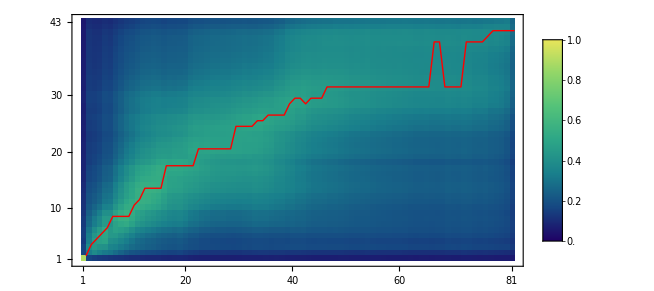

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData["BlueGreenYellow"][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}],Epilog->{Red,Line[MapIndexed[{#2[[1]],Ordering[#1,-1][[1]]}&,Transpose@mat]]},DataReversed->True]
```

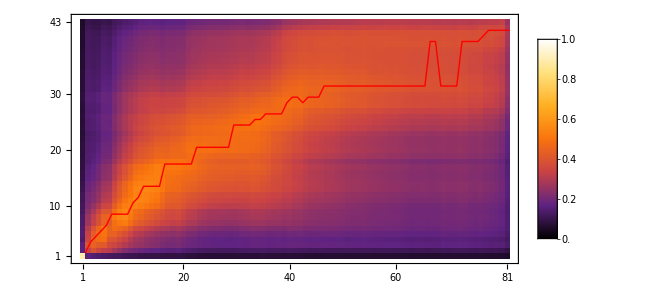

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData["SunsetColors"][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}],Epilog->{Red,Line[MapIndexed[{#2[[1]],Ordering[#1,-1][[1]]}&,Transpose@mat]]},DataReversed->True]
```

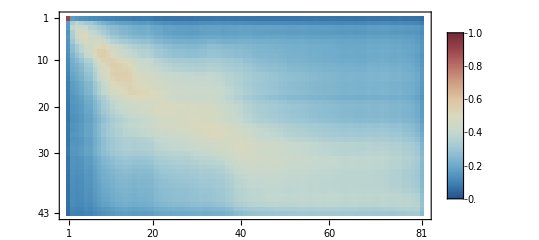

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData[{"RedBlueTones","Reverse"}][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

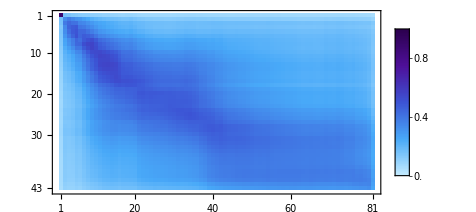

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData[{"DeepSeaColors","Reverse"}][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

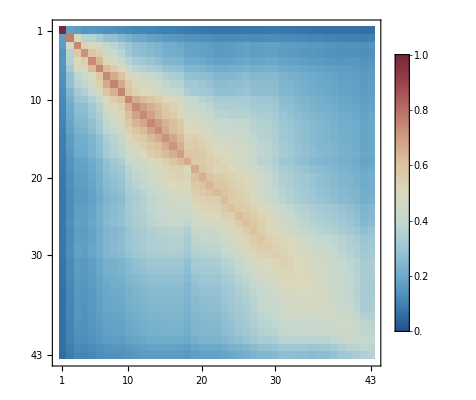

```mathematica
MatrixPlot[mat,ColorFunction->(ColorData[{"RedBlueTones","Reverse"}][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

```mathematica
Mean[MapThread[N@*Length@*Intersection,{knn1[[10]],knn2[[20]]}]]/10
```

```mathematica
Mean[MapThread[N@*Length@*Intersection,{knn1[[10]],knn2[[20]]}]]/10
```

0.365186

## Scratch space

### Parquet

```mathematica
t=Import[FileNameJoin[{projectDirectory,"knn",getDatasetName[{"google/gemma-2-2b","web_text"}]}],"Parquet"];
```

```mathematica
knnP=Transpose@NumericArray[Normal@t[[All,"knn"]]]
```

NumericArray[<27,2048,2047>, UnsignedInteger16]

```mathematica
embs=getDatasetEmbeddings[{"google/gemma-2-2b","web_text"}];
```

```mathematica
Length@Normal@embs[[10]]
```

2048

```mathematica
CountDistinct@Normal@embs[[10]]
```

2048

```mathematica
knn=getKNN[Normal@embs,100];
```

```mathematica
knnP2=Normal@knnP[[All,All,;;100]];
```

```mathematica
getKNN[embs_,k_]/;ArrayDepth[embs]===2:=Map[e|->TakeLargest[e->"Index",k],embs.Transpose[embs]-Normal[99999999*IdentityMatrix[Length[embs]]]]
getKNN[embs_,k_]/;ArrayDepth[embs]===3:=getKNN[#,k]&/@embs
```

```mathematica
Reverse@Ordering[Normal[embs[[1]]].Normal[embs[[1,10]]],-100]
```

{373,350,10,1686,1265,938,720,557,247,1801,1687,911,687,284,1864,1610,647,2013,1476,539,1746,1393,1299,832,626,312,25,1827,1633,1151,1956,1723,914,2047,2045,2042,2041,2034,2032,2030,2028,2027,2020,2017,2011,2009,2007,2006,2005,2002,2000,1996,1994,1993,1992,1990,1987,1985,1984,1982,1980,1975,1974,1973,1966,1965,1962,1960,1959,1955,1953,1952,1951,1944,1943,1941,1940,1938,1937,1936,1934,1932,1928,1927,1924,1922,1921,1920,1918,1917,1916,1915,1914,1913,1911,1910,1908,1907,1906,1904}

```mathematica
knn[[10,500]]
```

{796,520,1839,459,765,196,1580,1927,1702,168,1230,106,784,718,158,1114,1490,1728,940,858,1236,1300,1845,1953,649,1654,652,1951,1846,917,100,915,1341,712,240,1268,1920,1307,1117,651,1856,959,1018,600,1157,1873,1494,76,177,1346,906,1305,37,1996,219,1841,655,1244,307,317,1619,1990,1721,1511,1591,661,1014,492,991,406,448,1395,433,141,531,1529,1179,9,426,1752,1816,1719,81,800,1431,1615,1084,866,1826,1089,1122,1818,566,956,116,1457,748,808,1911,1906}

```mathematica
knnP2[[10,500]]+1
```

{796,520,1839,459,765,196,1580,1927,1702,168,1230,106,784,718,158,1114,1490,1728,940,858,1236,1300,1845,1953,649,1654,652,1951,1846,917,100,915,1341,712,240,1268,1920,1307,1117,651,1856,959,1018,600,1157,1873,1494,76,177,1346,906,1305,37,1996,219,1841,655,1244,307,317,1619,1990,1721,1511,1591,661,1014,492,991,406,448,1395,433,141,531,1529,1179,9,426,1752,1816,1719,81,800,1431,1615,1084,866,1826,1089,1122,1818,566,956,116,1457,748,808,1911,1906}

```mathematica
knn[[2;;]]==knnP2[[2;;]]+1
```

False

```mathematica
knnP2[[5,100]]+1
```

{598,1753,1402,110,1845,492,765,868,182,1079,975,483,520,106,426,1011,878,1134,112,651,649,1279,37,1520,1514,76,111,1341,1433,1833,1359,1047,1236,61,1990,624,1348,902,800,459,1802,1070,969,1490,1585,1974,1621,1555,384,433,1268,648,64,1320,1664,309,1370,1913,1259,952,931,1781,1378,844,1987,2047,141,345,1036,1873,1574,1628,278,208,1238,498,1019,907,1328,1779,304,1288,1654,1607,476,4,1457,1611,1113,233,362,1319,207,1300,661,1714,9,867,1472,667}

```mathematica
knnP[[All,All,;;100]]
```

NumericArray[<27,2048,100>, UnsignedInteger16]

```mathematica
ByteCount@Transpose@NumericArray[Normal@t[[All,"knn"]]]
```

226381984

```mathematica
ByteCount[t]
```

234063591

### CKA

def cka(feats_A, feats_B, kernel_metric='ip', rbf_sigma=1.0, unbiased=False):
        """Computes the unbiased Centered Kernel Alignment (CKA) between features."""
        
        if kernel_metric == 'ip':
            # Compute kernel matrices for the linear case
            K = torch.mm(feats_A, feats_A.T)
            L = torch.mm(feats_B, feats_B.T)
        elif kernel_metric == 'rbf':
            # COMPUTES RBF KERNEL
            K = torch.exp(-torch.cdist(feats_A, feats_A) ** 2 / (2 * rbf_sigma ** 2))
            L = torch.exp(-torch.cdist(feats_B, feats_B) ** 2 / (2 * rbf_sigma ** 2))
        else:
            raise ValueError(f"Invalid kernel metric {kernel_metric}")

        # Compute HSIC values
        hsic_fn = hsic_unbiased if unbiased else hsic_biased
        hsic_kk = hsic_fn(K, K)
        hsic_ll = hsic_fn(L, L)
        hsic_kl = hsic_fn(K, L)

        # Compute CKA
        #print('hsic', hsic_kl)
        cka_value = hsic_kl / (torch.sqrt(hsic_kk * hsic_ll) + 1e-6)        
        return cka_value.item()

def hsic_biased(K, L):
    """ Compute the biased HSIC (the original CKA) """
    H = torch.eye(K.shape[0], dtype=K.dtype, device=K.device) - 1 / K.shape[0]
    return torch.trace(K @ H @ L @ H)

```mathematica
With[{h=IdentityMatrix[Length[k]]-1/Length[k]},
h.k==k-Mean@Flatten@k
]
```

False

```mathematica
hsic[k_,l_]:=
With[{h=IdentityMatrix[Length[k]]-1/Length[k]},
EchoFunction[Dimensions][(k.h)].Transpose[(l.h)]
]
```

```mathematica
k=RandomReal[{-1,1},{100,200}];
l=RandomReal[{-1,1},{100,200}];
```

```mathematica
hsic[k,l]
```

Dot::dotsh: Tensors {{-0.920148,0.725806,-0.451955,-0.156164,-0.647644,0.553555,0.66821,«37»,-0.885381,0.461144,-0.370748,0.103553,-0.709417,-0.705129,«150»},«49»,«50»} and {{99/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,«50»},«49»,«50»} have incompatible shapes.

{2}

Dot::dotsh: Tensors {{0.789945,-0.329501,0.562759,0.359426,-0.894556,0.404679,-0.152354,-0.97414,«36»,-0.557983,-0.0720391,-0.560405,-0.188122,0.246084,-0.0840189,«150»},{«1»},«48»,«50»} and {{99/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,«50»},«49»,«50»} have incompatible shapes.

Dot::dotsh: Tensors {{-0.920148,0.725806,-0.451955,-0.156164,-0.647644,0.553555,0.66821,«37»,-0.885381,0.461144,-0.370748,0.103553,-0.709417,-0.705129,«150»},«49»,«50»} and {{99/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,-1/100,«50»},«49»,«50»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Rewrite this as WL functions

Here's how you can rewrite the Python functions for Centered Kernel Alignment (CKA) and Hilbert-Schmidt Independence Criterion (HSIC) in the Wolfram Language: 
cka[featsA_,featsB_,kernelMetric_ : "ip",rbfSigma_ : 1.0,unbiased_ : False]:=
 Module[{K,L,hsicFn,hsicKK,hsicLL,hsicKL,ckaValue},
  
  (* Compute kernel matrices based on the metric *)
  {K,L}=Switch[kernelMetric,
    "ip",{featsA . Transpose[featsA],featsB . Transpose[featsB]},
    "rbf",{Exp[-(Norm /@ Outer[Subtract,featsA,featsA,1])^2/(2 rbSigma^2)],
      Exp[-(Norm /@ Outer[Subtract,featsB,featsB,1])^2/(2 rbSigma^2)]},
    _,Message[cka::invalidMetric,kernelMetric]; Return[$Failed]
  ];
  
  (* Select HSIC function *)
  hsicFn=If[unbiased,hsicUnbiased,hsicBiased];
  
  (* Compute HSIC values *)
  {hsicKK,hsicLL,hsicKL}=hsicFn @@@ {{K,K},{L,L},{K,L}};
  
  (* Compute CKA value *)
  ckaValue=hsicKL/(Sqrt[hsicKK hsicLL]+10^-6);
  ckaValue
]

hsicBiased[K_,L_]:=
 Module[{H},
  H=IdentityMatrix[Length[K]]-1/Length[K];
  Tr[Transpose[K].H.Transpose[L].H]
]

(* Define hsicUnbiased if needed, similar to hsicBiased *)Wolfram
To use these functions, ensure your input matrices featsA and featsB are properly formed. You can adjust the RBF sigma and kernel metric as needed. If you need an unbiased version of HSIC, you can implement hsicUnbiased similarly to hsicBiased. Let me know if you need further assistance!

### OLD

```mathematica
Import@getDatasetPath[{"google/gemma-2-9b","web_text"}]
```

{data-00000-of-00006.arrow,data-00001-of-00006.arrow,data-00002-of-00006.arrow,data-00003-of-00006.arrow,data-00004-of-00006.arrow,data-00005-of-00006.arrow,dataset_info.json,state.json}

```mathematica
getDatasetEmbeddings[{"google/gemma-2-9b","web_text"}]//EchoTiming//Dimensions
```

4.61218

{43,2048,3584}

```mathematica
t1=Developer`ToPackedArray@Import[
FileNameJoin[{getDatasetPath[{"google/gemma-2-9b","web_text"}],"data-00000-of-00006.arrow"}],
{"Data",All,2}
];//EchoTiming
```

1.33646

```mathematica
TabularStructure[t1]
```

```mathematica
arrowTest=Import[getDatasetPath[{"google/gemma-2-9b","web_text"}],"ArrowDataset"]
```

Import::general: Error creating dataset. Could not read schema from '/Users/christopher/Documents/unireps/outputs/google__gemma-2-9b---web_text/data-00000-of-00006.arrow'. Is th… file?: Could not open IPC input source '/Users/christopher/Documents/unireps/outputs/google__gemma-2-9b---web_text/data-00000-of-00006.arrow': Not an Arrow file

$Failed

```mathematica
gramMatrix[m_]:=m.Transpose[m]
```

```mathematica
rv[x_,y_]:=Norm[Transpose[x].y,"Frobenius"]^2/(Norm[Transpose[x].x,"Frobenius"]*Norm[Transpose[y].y,"Frobenius"])
```

```mathematica
embs1=getDatasetEmbeddings[{"google/gemma-2-9b","web_text"}];//EchoTiming
```

4.30615

```mathematica
embs2=getDatasetEmbeddings[{"google/gemma-2-9b-it","web_text"}];//EchoTiming
```

8.32576

```mathematica
gramMatrix[Normal@embs1[[1]]]//Dimensions//EchoTiming
```

0.11042

{2048,2048}

```mathematica
rv[gramMatrix@Normal@embs1[[1]],gramMatrix@Normal@embs2[[1]]]
```

0.999859

```mathematica
RepeatedTiming[Normal@embs1[[1]];]
```

{0.00623774,Null}

```mathematica
matRV=Table[rv[gramMatrix@Normal@embs1[[i]],gramMatrix@Normal@embs2[[j]]],{i,Length[embs1]},{j,Length[embs2]}];//EchoTiming
```

838.015

```mathematica
matRV[[7,10]]
```

0.9958

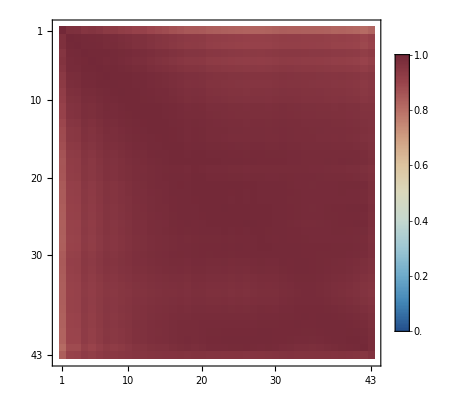

```mathematica
MatrixPlot[matRV,ColorFunction->(ColorData[{"RedBlueTones","Reverse"}][#]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}}]]
```

```mathematica
embs=Normal@getDatasetEmbeddings[{"google/gemma-2-9b","web_text"}];//EchoTiming
```

4.46294

```mathematica
Dimensions@embs
```

{43,2048,3584}

```mathematica
embs[[1]]
```

$Aborted

```mathematica
DistanceMatrix
```

```mathematica
Depth[]
```

```mathematica
ArrayDepth[embs]
```

3

```mathematica
IdentityMatrix[Length[embs[[1]]]]
```

IdentityMatrix[…]

```mathematica
knnMat=getKNN[embs,10];//EchoTiming
```

12.7174

```mathematica
knnMat//Dimensions
```

{43,3584,10}

```mathematica
Dimensions[embs[[1]].Transpose[embs[[1]]]]
```

{2048,2048}

```mathematica
Dimensions@embs
```

{43,2048,3584}

```mathematica
MinMax[embs[[1]].Transpose[embs[[1]]]]
```

{-0.286683,1.}

```mathematica
Dimensions[embs[[1]].Transpose[embs[[1]]]]
```

{2048,2048}

```mathematica
embs[[1]].Transpose[embs[[1]]]-99999*IdentityMatrix[Length[embs[[1]]]]
```

```mathematica
ByteCount@EchoTiming@getDatasetEmbeddings[{"google/gemma-2-9b","book_translations_en"}]
```

4.1349

1262485672

## OLD

```mathematica
Quit
```

```mathematica
Clear[m]
```

```mathematica
m=RandomReal[{0,1},{33,1024,4096}];
```

```mathematica
EchoTiming@Dimensions@Map[layer|->Map[e|->Ordering[e,-10],layer.Transpose[layer]],m]
```

2.21768

{33,1024,10}

```mathematica
Ordering[#,10]&/@(m[[1]].Transpose[m[[1]]])
```

```mathematica
m.Transpose[m]
```

```mathematica
ByteCount@m
```

1107296424